```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\jitter

```mathematica
tick=0.04;fontsize=44;
```

```mathematica
data1=Import["low_jitter_wide_image.csv","Table","FieldSeparators"->{";"}];
t1=Subdivide[-1.2*^-7,1.08*^-6,2000-1];
data2=Import["low_jitter.csv"];
```

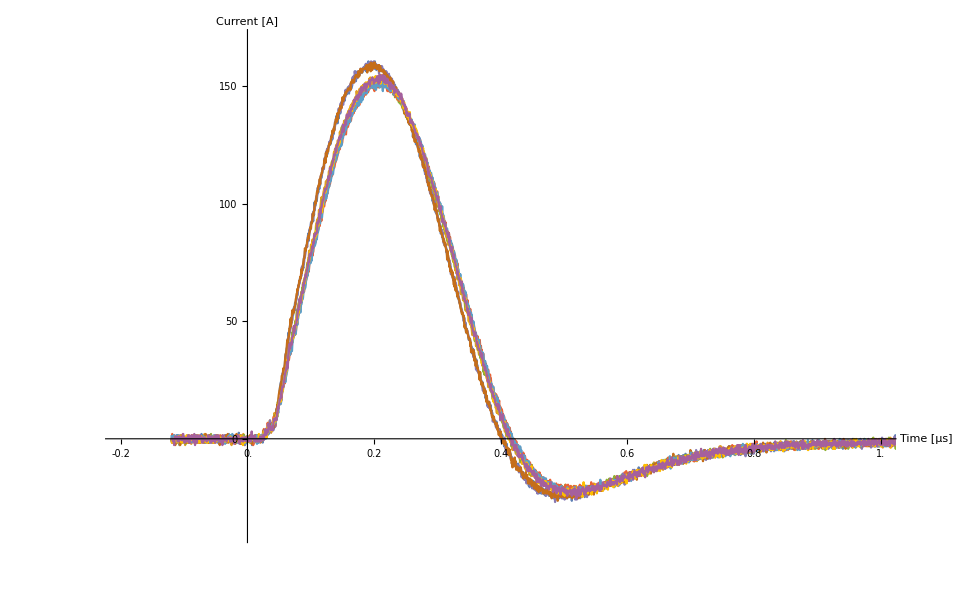

```mathematica
plot1=ListLinePlot[Table[Thread[{t,col⟦All,2⟧⟦j*2000+1;;(j+1)*2000⟧}],{j,3,11}]
,PlotStyle->Automatic,
TicksStyle->Directive[Black,FontSize->fontsize,FontFamily->"Helvetica"],
AxesStyle->{{Black,Thick},{Black,Thick}},
AxesLabel->{Style["Time [μs]",Black,FontSize->fontsize],Style["Current [A]",Black,FontSize->fontsize]},
Ticks->{
Table[{j*10^-6,j,tick,Directive[Thick]},{j,-0.2,1,0.2}],
Table[{j,10j,tick,Directive[Thick]},{j,-5,15,5}]
},ImageSize->960,PlotRange->{{-2*10^-7,1*10^-6},{-4,17}}]
```

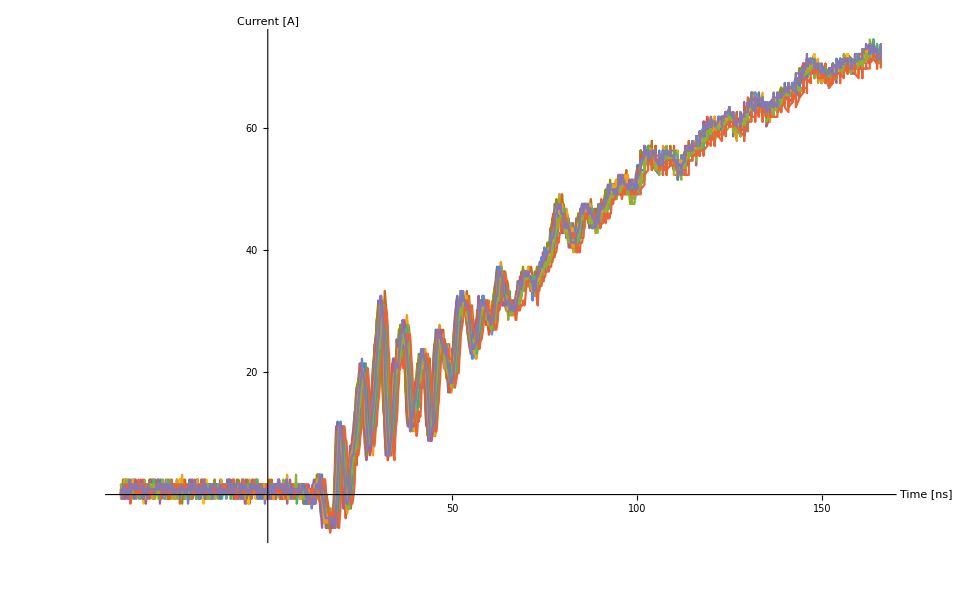

```mathematica
plot2=ListLinePlot[Table[
Thread[{data2⟦All,1⟧,data2⟦All,j⟧
}],{j,2,21}],PlotStyle->Automatic,
TicksStyle->Directive[Black,FontSize->fontsize,FontFamily->"Helvetica"],
AxesStyle->{{Black,Thick},{Black,Thick}},
AxesLabel->{Style["Time [ns]",Black,FontSize->fontsize],Style["Current [A]",Black,FontSize->fontsize]},
Ticks->{
{{5.*^-8,50,tick,Directive[Thick]},
{1*^-7,100,tick,Directive[Thick]},
{1.5*^-7,150,tick,Directive[Thick]}},
{{2,20,tick,Directive[Thick]},{4,40,tick,Directive[Thick]},{6,60,tick,Directive[Thick]}}
},ImageSize->960]
```

```mathematica
color=Lighter[Black,0.3];
```

```mathematica
inset=Show[{GraphicsColumn[{plot1,plot2},PlotRange->All,ImageSize->960],Graphics[{
{EdgeForm[{Thick,color}],FaceForm[],Rectangle[ImageScaled[{0.26,0.02}],ImageScaled[{0.75,0.39}]]}
,
{EdgeForm[{Thick,color}],FaceForm[],Rectangle[ImageScaled[{0.2,0.61}],ImageScaled[{0.23,0.64}]]}
,
{Thick,color,Line[{ImageScaled[{0.2,0.61}],ImageScaled[{0.26,0.02}]}]}
,
{Thick,color,Line[{ImageScaled[{0.75,0.39}],ImageScaled[{0.23,0.64}]}]}
}]}]
```

-Graphics-

```mathematica
Export["low_jitter.png",inset]
Export["low_jitter.pdf",inset]
```

low_jitter.png

low_jitter.pdf

```mathematica
SystemOpen["low_jitter.png"]
```